Piecewise[{{33523081420369092505059849428816621759109070346137696779260225128288162528813601984030474874189447952835482888240187058921735603854740388474430397816996057520474834020079500585819257432789719307549919580543995165607730456882358325538862658894192101295325396355475781914790287483409142504030815180000 (1-x)^433 x^567, 0<x<1}, {0, True}}]

Piecewise[{{BetaRegularized[x,568,434], 0<x<1}, {1, x≥1}, {0, True}}]

ConditionalExpression[InverseBetaRegularized[x,568,434],0≤x≤1]

284/501

0.498866

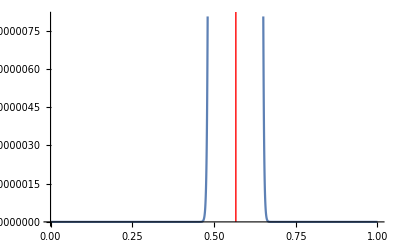

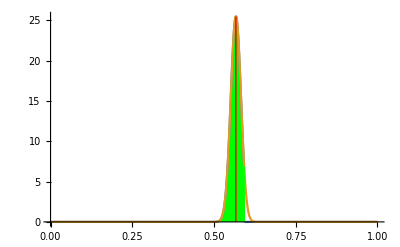

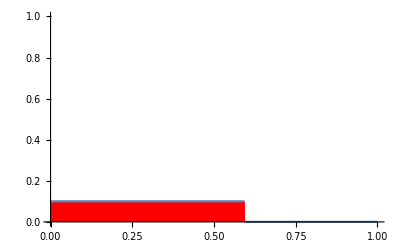

{0.,0.592527}

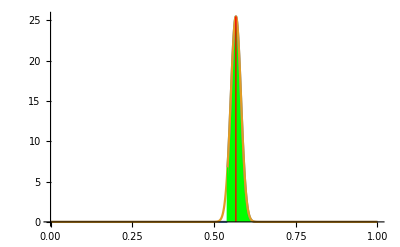

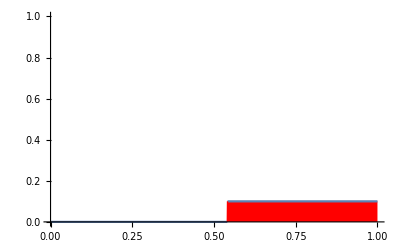

{0.541053,1}

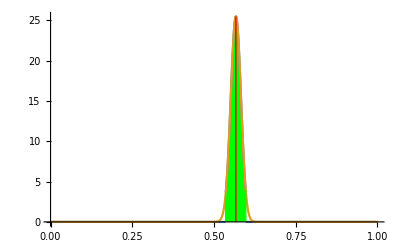

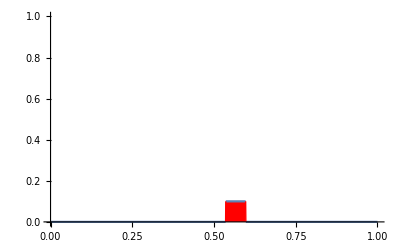

{0.535769,0.597105}

```mathematica
(*β-fordelingen *)
(*Sett inn σ*) 
a:=568;
(*Sett inn μ*) 
b:=434;
(*Velg størrelsen på konfidensintervallet*)
konfint := 0.95;
(*For endringer på intervallet, normalt skal denne bare stå på 0 til 1*)
Nedre := 0.0;
Ovre := 1.0;

(*Her trenger man ikke gjøre endringer*)
Temp:=BetaDistribution[a,b];
f[t_]:=PDF[Temp,t];
F[t_]:=CDF[Temp,t];
Ff[t_]:=InverseCDF[Temp,t];
theInterval[t_,start_,end_]:=UnitStep[t-Ff[start]] (1-UnitStep[t-Ff[1-end]])
cF[t_,start_,end_]:=f[t] theInterval[t,start,end];
ciPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,Nedre,Ovre},PlotRange->All,Filling->{1->{Axis,{Green}},2->{{1},{White}}}]
ciIPlot[start_,end_,range_]:=Plot[0.1 theInterval[x,start,end],{x,Nedre,Ovre},PlotRange->{Nedre,Ovre},Filling->{1->{Axis,{Red}}}]
cendPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,0,1},PlotRange->All,Filling->{1->{Axis,{White}},2->{{1},{Red}}}]
f[x]
F[x]
Ff[x]
Mean[Temp]
F[Mean[Temp]]//N
Show[Plot[f[t],{t,Nedre,Ovre}],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]]

(*Venstre intervall*)

Show[
ciPlot[0,1-konfint,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[0,1-konfint,0.03]
{Ff[0.0],Ff[konfint]}

(*Høyre intervall*)
Show[
ciPlot[1-konfint,0,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[1-konfint,0,0.03]
{Ff[1-konfint],Ff[1]}

(*Symetriskkonfidensintervall om μ*)
Show[
ciPlot[F[Mean[Temp]]-konfint/2,1-konfint/2-F[Mean[Temp]],0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[F[Mean[Temp]]-konfint/2,1-konfint/2-F[Mean[Temp]],0.03]
{Ff[F[Mean[Temp]]-konfint/2],Ff[F[Mean[Temp]]+konfint/2]}
```